## 1. Rolling wheel as a rigid body motion

```mathematica
Clear[g,R,θ,v0,hmax];
(*With respect to ICZV:*)
xP[θ_]:=-R*Sin[θ];
yP[θ_]:=R*(1-Cos[θ]);
vPx[θ_]:=v0*(1-Cos[θ]);
vPy[θ_]:=v0*Sin[θ];
```

```mathematica
(*ballistic trajectory for given θ:*)
y[x_,θ_]:=yP[θ]+(x-xP[θ])*Sin[θ]/(1-Cos[θ])-g*(x-xP[θ])^2/(2 v0^2(1-Cos[θ])^2);

(*xm[θ_] corresponds to ymax for given θ:*)
Simplify[Solve[D[y[x,θ],x]==0,x],R>0&&v0>0]
xm[θ_]:=-((g R-v0^2+v0^2 Cos[θ]) Sin[θ])/g;
```

{{x→-((g R-v0^2+v0^2 Cos[θ]) Sin[θ])/g}}

h with coordinate y

```mathematica
(*ymax for given θ: *)
ymax[θ_]:=Simplify[y[x,θ]/.x->xm[θ]];
ymax[θ];
Simplify[D[ymax[θ],θ]]
(*h is max of ymax: *)
h=Simplify[R-R cosθ+(v0^2 (1-cosθ^2))/(2 g)/.cosθ->(-R*g)/v0^2]
(*check*)Simplify[h-(R+v0^2/(2 g)+(R^2 *g)/(2 v0^2))]
```

(R+(v0^2 Cos[θ])/g) Sin[θ]

((g R+v0^2)^2)/(2 g v0^2)

0

h with Galilei’s eq

```mathematica
ym[θ_]:=vPy[θ]^2/(2*g)+yP[θ];
Simplify[D[ym[θ],θ]]
ym[θ_]:=R (1-cosθ)+(v0^2 (1-cosθ^2))/(2 g);
h=Simplify[ym[θ]/.cosθ->-(R*g)/v0^2]
(*check*)Simplify[h-(R+v0^2/(2 g)+(R^2 *g)/(2 v0^2))]
```

(R+(v0^2 Cos[θ])/g) Sin[θ]

((g R+v0^2)^2)/(2 g v0^2)

0

```mathematica
v0=6;g=1;R=10.;θ=2*Pi/4.;
```

{{x→-24.1945},{x→93.361}}

-2.84217×10^-14

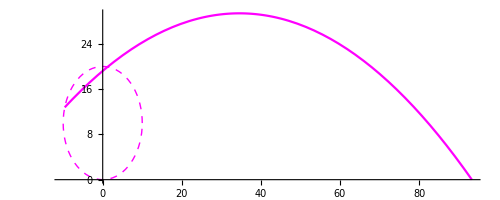

```mathematica
θm=ArcCos[(-R*g)/v0^2];(* value of θ for h (max height)*)
θ=2*θm/2; (*! redifined θ for h (max height)*)
solx=Simplify[Solve[y[x,θ]==0,x]]
solx[[2,1,2]];
y[solx[[2,1,2]],θ](*check intersection with X axis*)
xP[θ];
xP[θ];
g0=Plot[y[x,θ],{x,xP[θ],solx[[2,1,2]]},PlotStyle->Magenta];
g1=Graphics[{Magenta,Dashed,Circle[{0,R},R],Axes->True}];
Show[g0,g1,PlotRange->All,AspectRatio->Automatic,AxesOrigin->{0,0}]
```

## 2. Cycloidal method

```mathematica
Clear[g,R,θ,v0];
(*θ is the detaching angle*)
XP[θ_]:=R*(θ-Sin[θ]);
YP[θ_]:=R*(1-Cos[θ]);
vPX[θ_]:=v0*(1-Cos[θ]);
vPY[θ_]:=v0*Sin[θ];
w[θ_]:=2*v0*Sin[θ/2];
XT[θ_]:=R(1-Cos[θ]);
YT[θ_]:=R(Sin[θ]);
α0[θ_]:=ArcTan[Cot[θ/2]];
(*C4 or C5?, p.12: uniform motion of the wheel with speed v0=>
vP=R*θ̇=2*v0*Sin[θ/2]*)
```

```mathematica
(*ballistic trajectory for given θ*)
Y[X_,θ_]:=YP[θ]+(X-XP[θ])*vPY[θ]/vPX[θ]-g*(X-XP[θ])^2/(2 v0^2(1-Cos[θ])^2);
Y[X_,θ_]:=YP[θ]+(X-XP[θ])*Sin[θ]/(1-Cos[θ])-g*(X-XP[θ])^2/(2 v0^2(1-Cos[θ])^2);
```

{{X→-5.67178},{X→111.884}}

-2.84217×10^-14

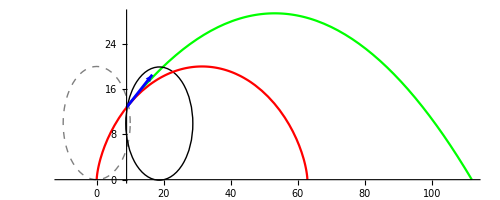

```mathematica
v0=6;g=1;R=10.;θ=2*Pi/4.;
θm=ArcCos[(-R*g)/v0^2];
θ=2*θm/2; (*! redifined θ for h (max height)*)
solX=Simplify[Solve[Y[X,θ]==0,X]]
solX[[2,1,2]];
Y[solX[[2,1,2]],θ](*check intersection with X axis*)
XP[θ];
YP[θ];
C1T[θ_]:={XT[θ],YT[θ]};
C1[θ_]:={XP[θ],YP[θ]};

p0=Plot[Y[X,θ],{X,XP[θ],solX[[2,1,2]]},PlotStyle->Green];
p1=Graphics[{Gray,Dashed,Circle[{0,R},R],Axes->True}];
p2=Graphics[Circle[{R*θ,R},R],Axes->True];
p3=ParametricPlot[{XP[a],YP[a]},{a,0,4/2 π},PlotStyle->Red];
p4=Graphics[{ Blue,Thickness[0.005],Arrowheads[Medium],Rotate[Arrow[{C1[θ],{w[θ]+C1[θ][[1]],C1[θ][[2]]}}],α0[θ],C1[θ]]}];
(*p4=Graphics[{Blue, Thickness[0.005],Arrowheads[Medium],Arrow[{C1[θ],(C1[θ]+C1T[θ])}]}];*)
Show[p0,p1,p2,p3,p4,PlotRange->All,AspectRatio->Automatic]
```

For animation

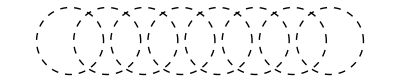

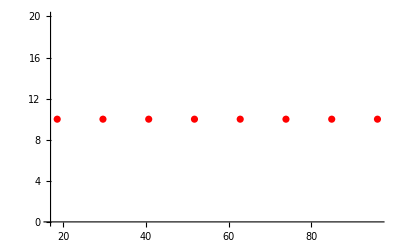

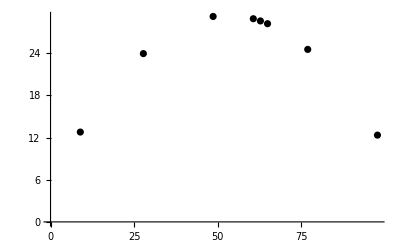

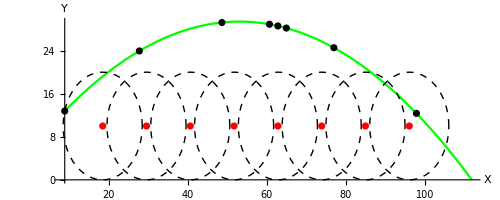

```mathematica
(* Xp[n_] is X on parabola:*)
Xp[n_]:=R*(Xc[n]/R-Sin[Xc[n]/R]);
(* Xc[n_] is X for center of circle:*)
Xc[n_]:=R*θ+n*(-R*θ+2*π*R)/4;TabC1=Graphics[{Dashed,Table[
Circle[{Xc[n],R},R],{n,0,7}]}]
TabC2=ListPlot[Table[
{Xc[n],R},{n,0,7}], PlotStyle->{Red}]
TabP=ListPlot[Table[{Xp[n],Y[Xp[n],θ]},{n,0,7}], PlotStyle->{Black}]
Show[p0,TabC1,TabC2,TabP, AspectRatio->Automatic,AxesLabel-> {Style["X",Italic],Style["Y",Italic]},PlotRange->All]
```

## 3. Equivalence of trajectories

```mathematica
(*check the equivalence of trajectories in with X->x-R*θ, XP[θ]->xP[θ]-R*θ*)
Clear[YP,yP,XP,xP,θ,v0];
Y[X,θ]
Simplify[Y[X,θ]/.YP[θ]->yP[θ]/.XP[θ]->xP[θ]-R*θ/.X->x-R*θ]
```

(Sin[θ] (X-XP[θ]))/(1-Cos[θ])-(X-XP[θ])^2/(2 v0^2 (1-Cos[θ])^2)+YP[θ]

Cot[θ/2] (x-xP[θ])-(Csc[θ/2]^4 (x-xP[θ])^2)/(8 v0^2)+yP[θ]

```mathematica
y[x_,θ_]:=yP[θ]+(x-xP[θ])*Sin[θ]/(1-Cos[θ])-g*(x-xP[θ])^2/(2 v0^2(1-Cos[θ])^2);
a=Simplify[y[x,θ]/.yP[θ]->YP[θ]/.xP[θ]->XP[θ]-R*θ/.x->X-R*θ];
Simplify[a-Y[X,θ]]
```

0